# Analysis of 3-mode Transducer

## Shoumik Chowdhury (@shoumikdc); 8/11/2020

## Setup and Initialization

### Preliminary Definitions

```mathematica
Id[n_]:=IdentityMatrix[n] 
mJn[n_]:=ArrayFlatten[Id[n]⊗({{0, 1}, {-1, 0}})] ; (* Symplectic J matrix in QP basis *)
mJqqn[n_] :=ArrayFlatten[({{0, 1}, {-1, 0}})⊗Id[n]]; (*Symplectic J matrix in QQ basis *)
sympQn[n_, mS_]:=1-Norm[mSᵀ.mJn[n].mS-mJn[n]]; (* Test for symplecticity *)

n = 3;  (*Number of modes*)
mJ = mJn[n];
sympQ[mS_] := sympQn[n, mS]
QQtoQP[n0_,M0_]:=Module[{n=n0,M=M0},
(*Converts a symplectic matrix from qqpp basis to qpqp basis *)
ord=Flatten[Table[{i,n+i},{i,1,n}]];
M⟦ord,ord⟧
]
QPtoQQ[n0_,M0_]:=Module[{n=n0,M=M0},
(*Converts a symplectic matrix from qpqp basis to qqpp basis *)
odds=Table[{i},{i,1,2 n,2}];
evens=Table[{i+1},{i,1,2 n,2}];
ord=Flatten[Join[odds,evens]];
M⟦ord,ord⟧
]

(* Generate random symmetric and random symplectic matrices in qpqp basis *) 
rSymMat[{a_,b_},c_]:=(UpperTriangularize[#]+UpperTriangularize[#,1]ᵀ)&@RandomReal[{a,b},{c,c}];
rSympMat[a_,b_,n_]:=QQtoQP[n,Id[2 n]-Inverse[(mJqqn[n].rSymMat[{a,b},2 n]+1/2 Id[2 n])]];
(* Output formatting to display conjugates with an asterisk *)
Unprotect[Conjugate];
Conjugate/:MakeBoxes[Conjugate[x_],StandardForm]:=TemplateBox[{Parenthesize[x,StandardForm,Power]},"Conjugate",DisplayFunction->(SuperscriptBox[#1,"*"]&)]
Protect[Conjugate];
```

# Transducer Initialization and Decoupling Functions

```mathematica
generateMS[Δo_,ωm_,Δμ_, gom_,gμm_,goμ_]:= 
Module[{κo=1,κm=1,κμ=1,κb=1, T,M,Y,W,SComplex},
T[ω0_]:=I ({{ω0, 0, 0, 0, 0, 0}, {0, ω0, 0, 0, 0, 0}, {0, 0, ω0, 0, 0, 0}, {0, 0, 0, ω0, 0, 0}, {0, 0, 0, 0, ω0, 0}, {0, 0, 0, 0, 0, ω0}})- I({{-Δo+(ⅈ κo)/2, -gom, -goμ, 0, -Conjugate[gom]/2, 0}, {-Conjugate[gom], -ωm+(ⅈ κm)/2, -gμm, -Conjugate[gom]/2, 0, -Conjugate[gμm]/2}, {-Conjugate[goμ], -Conjugate[gμm], -Δμ+(ⅈ κμ)/2, 0, -Conjugate[gμm]/2, 0}, {0, gom/2, 0, Δo+(ⅈ κo)/2, Conjugate[gom], Conjugate[goμ]}, {gom/2, 0, gμm/2, gom, ωm+(ⅈ κm)/2, Conjugate[gμm]}, {0, gμm/2, 0, goμ, gμm, Δμ+(ⅈ κμ)/2}});
M = ({{T[ω], 0}, {0, T[-ω]}}) // ArrayFlatten;
Y = ({{√κo, 0, 0, 0, 0, 0}, {0, √κm, 0, 0, 0, 0}, {0, 0, √κμ, 0, 0, 0}, {0, 0, 0, √κo, 0, 0}, {0, 0, 0, 0, √κm, 0}, {0, 0, 0, 0, 0, √κμ}});
W = ({{Y, 0}, {0, Y}}) // ArrayFlatten;
U = 1/(√2)({{1, I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, I, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, I, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -I, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, -I, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -I}, {0, 0, 0, 0, 0, 0, 1, I, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, I, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, I}, {1, -I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -I, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -I, 0, 0, 0, 0, 0, 0}});
(* In the case that ω -> 0, we can simplify the problem to a 6×6 matrix *)
U6 = 1/(√2)({{1, I, 0, 0, 0, 0}, {0, 0, 1, I, 0, 0}, {0, 0, 0, 0, 1, I}, {1, -I, 0, 0, 0, 0}, {0, 0, 1, -I, 0, 0}, {0, 0, 0, 0, 1, -I}});
SComplex = Id[6] - Y.Inverse[T[ω]].Y;
{Inverse[U6].SComplex.U6, T[ω]}
]

DecoupleQ[mS_,n_,mode_, rescale_]:=
(*This is a wrapper function to compute the local operations to decouple Q given input mS.We rotate column c->row r*)Module[{cv,rv,ncv,nrv,mL,c=2 mode-1,r=2 mode-1},(*Tabular representations of column vector cv and row vectow rv in qpqp basis*)cv=Table[{mS⟦i,c⟧,mS⟦i+1,c⟧},{i,1,2 n,2}];
rv=Table[{mS⟦r,i⟧,mS⟦r,i+1⟧},{i,1,2 n,2}];
(*we are going to rotate column c->row r*)
ncv=Norm/@cv/.0->1;(*list of norms of cv*)
nrv=Norm/@rv/.0->1;(*list of norms of rv*)
mL=
Table[(({{rv⟦i,1⟧, -rv⟦i,2⟧}, {rv⟦i,2⟧, rv⟦i,1⟧}})/nrv⟦i⟧).({{nrv⟦i⟧/(rescale*ncv⟦i⟧), 0}, {0, (rescale*ncv⟦i⟧)/nrv⟦i⟧}}).(({{cv⟦i,1⟧, cv⟦i,2⟧}, {-cv⟦i,2⟧, cv⟦i,1⟧}})/ncv⟦i⟧),{i,1,n}]/.({{0, 0}, {0, 0}})->({{1, 0}, {0, 1}}) ;(*List of local symplectic operations for all modes*)

ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@mL]]
]

DecoupleP[mS_,n_,mode_]:=
(*This is a wrapper function to compute the local operations to decouple P quadrature given input symplectic mS. We rotate column c->row r*)Module[{cv,rv,ncv,nrv,mL,c=2 mode,r=2 mode},(*Tabular representations of column vector cv and row vectow rv in qpqp basis*)cv=Table[{mS⟦i,c⟧,mS⟦i+1,c⟧},{i,1,2 n,2}];
rv=Table[-{mS⟦r,i⟧,mS⟦r,i+1⟧},{i,1,2 n,2}];
rv⟦mode,1⟧=-rv⟦mode,1⟧;(*we are going to rotate column c->row r*)
ncv=Norm/@cv/.0->1;nrv=Norm/@rv/.0->1;
mL = Table[(({{rv⟦i,1⟧, -rv⟦i,2⟧}, {rv⟦i,2⟧, rv⟦i,1⟧}})/nrv[[i]]).({{nrv⟦i⟧/ncv⟦i⟧, 0}, {0, ncv⟦i⟧/nrv⟦i⟧}}).(({{cv⟦i,1⟧, cv⟦i,2⟧}, {-cv⟦i,2⟧, cv⟦i,1⟧}})/ncv[[i]]),{i,1,n}]/.({{0, 0}, {0, 0}})->({{1, 0}, {0, 1}});
mL⟦mode⟧=-mL⟦mode⟧;
ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@mL]]
]
```

### (Pre)-Iwasawa Decomposition

```mathematica
Iwasawa[n0_, mS0_] := Module[{mS = mS0, n = n0}, 
(* Method for calculating the Iwasawa decomposition of a 2n×2n symplectic matrix in QQPP basis.Given an input matrix, we find K,A, and N such that mS=K*A*N.Based on Matlab algorithm: Benzi M.and Razouk N.2007. On the Iwasawa decomposition of a symplectic matrix. 
Applied Mathematics Letters,20 (3),pp .260-265. http: //www.mathcs.emory.edu/~benzi/Web_papers/iwasawa.pdf *)

S11 = mS⟦1;;n, 1;;n⟧;
S21 = mS⟦n+1;; 2n, 1;;n⟧;
S1=ArrayFlatten[{{S11},{S21}}];
{Q, R} = QRDecomposition[S1]; Q = Transpose[Q];
Q11 = Q⟦1;;n, 1;;n⟧;
Q21 = Q⟦n+1;;2n,  1;;n⟧;

H = DiagonalMatrix[Diagonal[R]]; 
U = Inverse[H].R;
h = Sign[Diagonal[H]];

SqrtD=DiagonalMatrix[h*Diagonal[H]];InvSqrtD=DiagonalMatrix[1/(h*Diagonal[H])];
h=ArrayFlatten[Table[h,{i,1,n}]];

K11 = Q11*h;
K12 = -Q21*h;
Amat = ArrayFlatten[{{SqrtD, 0}, {0, InvSqrtD}}];
Kmat = ArrayFlatten[{{K11, K12}, {-K12, K11}}];
S1 = mS⟦1;;2n, n+1;;2n⟧;
N1 = (Inverse[Amat].Transpose[Kmat]).S1;
Nmat = ArrayFlatten[{{U, N1⟦1;;n, 1;;n⟧}, {0, N1⟦n+1;;2n, 1;;n⟧}}];
{Kmat, Amat, Nmat}
]

preIwasawa[n0_,mS0_]:=Module[{mS=mS0,n=n0},
(*Method for calculating the pre-Iwasawa decomposition of a 2n×2n symplectic matrix in QQPP basis. *)
Am = mS⟦1;;n, 1;;n⟧;
Bm = mS⟦1;;n, n+1;;2n⟧;
Cm=mS⟦n+1;;2 n,1;;n⟧;
Dm = mS⟦n+1;;2n, n+1;;2n⟧;

L = MatrixPower[Am.Transpose[Am] + Bm.Transpose[Bm], 1/2];
InvL = Inverse[L];
X = InvL.Am;
Y = InvL.Bm;
P = (Cm.Transpose[Am] + Dm.Transpose[Bm]).(InvL.InvL);

mQND= ArrayFlatten[{{Id[n], 0}, {P, Id[n]}}];
mZ = ArrayFlatten[{{L, 0}, {0, InvL}}];
mBS = ArrayFlatten[{{X, Y}, {-Y, X}}];

{mQND, mZ, mBS}
]
```

### Pre-Iwasawa Plotting Functions

```mathematica
preIwasawaPlotQND[mS0_]:=
Module[{mS=mS0, mL1, mS1, mL2, mS2},
mL1=DecoupleQ[mS,3,2];
     mS1=mS.mJ.mL1.mS;
     mL2=DecoupleP[mS1,3,2];
     mS2=mS1.mJ.mL2.mS1;
(*mRes = QPtoQQ[2, mS2⟦3;;, 3;;⟧];*)
mRes = QPtoQQ[2, ArrayFlatten[({{mS2⟦1;;2, 1;;2⟧, mS2⟦1;;2, 5;;6⟧}, {mS2⟦5;;6, 1;;2⟧, mS2⟦5;;6, 5;;6⟧}})]];
{mQND,mZ,mBS}=preIwasawa[2,mRes];

P = mQND⟦3;;4, 1;;2⟧;
(P⟦1, 2⟧)^2 + (P⟦2, 1⟧)^2
(*Norm[P]*)
]
preIwasawaPlotZ[mS0_]:=
Module[{mS=mS0, mL1, mS1, mL2, mS2},
mL1=DecoupleQ[mS,3,2];
     mS1=mS.mJ.mL1.mS;
     mL2=DecoupleP[mS1,3,2];
     mS2=mS1.mJ.mL2.mS1;
(*mRes = QPtoQQ[2, mS2⟦3;;, 3;;⟧];*)
mRes = QPtoQQ[2, ArrayFlatten[({{mS2⟦1;;2, 1;;2⟧, mS2⟦1;;2, 5;;6⟧}, {mS2⟦5;;6, 1;;2⟧, mS2⟦5;;6, 5;;6⟧}})]];
{mQND,mZ,mBS}=preIwasawa[2,mRes];

L = mZ⟦1;;2, 1;;2⟧;
((L.Transpose[L])⟦1, 2⟧)^2+ ((L.Transpose[L])⟦2,1⟧)^2

]
preIwasawaPlotBS[mS0_]:=
Module[{mS=mS0, mL1, mS1, mL2, mS2},
mL1=DecoupleQ[mS,3,2];
     mS1=mS.mJ.mL1.mS;
     mL2=DecoupleP[mS1,3,2];
     mS2=mS1.mJ.mL2.mS1;
(*mRes = QPtoQQ[2, mS2⟦3;;, 3;;⟧];*)
mRes = QPtoQQ[2, ArrayFlatten[({{mS2⟦1;;2, 1;;2⟧, mS2⟦1;;2, 5;;6⟧}, {mS2⟦5;;6, 1;;2⟧, mS2⟦5;;6, 5;;6⟧}})]];
{mQND,mZ,mBS}=preIwasawa[2,mRes];
mBSqp = QQtoQP[2, mBS];
(√(mBSqp⟦1, 1⟧^2 + mBSqp⟦1, 2⟧^2))^2
]
```

## Analysis and Testing

### ################ ######## See here for testing the c parameter #######################

```mathematica
(* param order: [Δo_,ωm_,Δμ_, gom_,gμm_,goμ_] *)
{mS, T} = generateMS[1, 1, 1,0.5, 1.175, 0] /. ω -> 0;
mS=Re[N[mS]];
N[mS]//MatrixForm
sympQ[mS]
```

(1.12719 | -0.359982 | -1.22873 | -0.938151 | 1.2389 | 1.03404
1.58871 | 1.12719 | -2.10045 | -1.22873 | 1.85346 | 1.2389
-1.22873 | -0.938151 | 4.0386 | 2.07002 | -2.88751 | -2.20466
-2.10045 | -1.22873 | 5.94435 | 4.0386 | -4.93606 | -2.88751
1.2389 | 1.03404 | -2.88751 | -2.20466 | 3.51141 | 1.63
1.85346 | 1.2389 | -4.93606 | -2.88751 | 5.15564 | 3.51141)

1.

```mathematica
rescale = 1;
mL1=DecoupleQ[mS,3,2,rescale]; (* The last parameter here is "rescale": this is the c parameter *)
mS1=mS.mJ.mL1.mS;
Chop[mS1,10^-10]//MatrixForm
```

(0.55056 | 0.204104 | 0 | -0.0163237 | -0.192946 | 0.341116
-0.28506 | 1.47627 | 0 | -0.00805303 | -0.261139 | -0.207139
0 | 0 | 0 | 1. | 0 | 0
-0.015453 | 0.00805303 | -1. | 0.984249 | -0.0363146 | 0.0189246
-0.192946 | 0.341116 | 0 | -0.0383608 | 0.179242 | 0.86057
-0.261139 | -0.207139 | 0 | -0.0189246 | -0.787614 | 1.07763)

```mathematica
(* TESTING DECOUPLE P in the main notebook for the case above *)

mode = 2;
c = 4; (* column *) 
r = 4; (* row *)

gamma = mS1⟦;;, 4⟧;
alpha = mS1⟦3, ;;⟧;
beta = mS1⟦4, ;;⟧;
newrow =rescale^2*beta -(rescale^-1 + rescale)*mS1⟦4, 4⟧*alpha;

rv = Table[{newrow[[i]], newrow[[i+1]]}, {i, 1, 2n, 2}];
cv = Table[{gamma[[i]],gamma[[i+1]]},{i,1,2 n,2}];

(* This is what's currently in "DecoupleP"; I've commented it out. 
cv=Table[{mS1⟦i,c⟧,mS1⟦i+1,c⟧},{i,1,2 n,2}];
rv=Table[-{mS1⟦r,i⟧,mS1⟦r,i+1⟧},{i,1,2 n,2}];
rv⟦mode,1⟧=-rv⟦mode,1⟧;
*)

ncv=Norm/@cv/.0->1;nrv=Norm/@rv/.0->1;
mL = Table[(({{rv⟦i,1⟧, -rv⟦i,2⟧}, {rv⟦i,2⟧, rv⟦i,1⟧}})/nrv[[i]]).({{nrv⟦i⟧/ncv⟦i⟧, 0}, {0, ncv⟦i⟧/nrv⟦i⟧}}).(({{cv⟦i,1⟧, cv⟦i,2⟧}, {-cv⟦i,2⟧, cv⟦i,1⟧}})/ncv[[i]]),{i,1,n}]/.({{0, 0}, {0, 0}})->({{1, 0}, {0, 1}});

(*mL⟦mode⟧=-mL⟦mode⟧; also commenting this out*)

(testML2 = ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@mL]]);

(mS2 = Chop[mS1.mJ.testML2.mS1, 10^-10])// MatrixForm
```

(-0.248622 | 0.230889 | 0 | 0 | 0.36718 | -0.683975
0.0102445 | -2.03721 | 0 | 0 | 0.527423 | 0.368011
0 | 0 | 0 | 1. | 0 | 0
0 | 0 | -1. | 1.9685 | 0 | 0
0.36718 | -0.683975 | 0 | 0 | 0.458005 | -1.0854
0.527423 | 0.368011 | 0 | 0 | 1.02525 | -1.32898)

### ##################################### END TESTING ####################################

## SVD Classification

```mathematica
(*mL1 = DecoupleQ[mS,3,2, 1];
mS1=mS.mJ.mL1.mS;
mL2=DecoupleP[mS1,3,2];
mS2=mS1.mJ.mL2.mS1;
sympQ[mS2]
Chop[mS2,10^-10]//MatrixForm*)
mRes = ArrayFlatten[({{mS2⟦1;;2, 1;;2⟧, mS2⟦1;;2, 5;;6⟧}, {mS2⟦5;;6, 1;;2⟧, mS2⟦5;;6, 5;;6⟧}})];
(*extract resultant 4×4 subblock*)
mRes//MatrixForm
sympQn[2,mRes]
```

(-0.248622 | 0.230889 | 0.36718 | -0.683975
0.0102445 | -2.03721 | 0.527423 | 0.368011
0.36718 | -0.683975 | 0.458005 | -1.0854
0.527423 | 0.368011 | 1.02525 | -1.32898)

1.

```mathematica
{MatrixRank[mRes⟦3;;4, 1;;2⟧], MatrixRank[mRes⟦3;;4, 3;;4⟧]}
Det[(mRes)⟦3;;4, 1;;2⟧]
Det[(mRes)[[3;;4,3;;4]]]
```

{2,2}

0.495871

0.504129

## Iwasawa Plots

```mathematica
{mQND, mZ, mBS} = preIwasawa[2, mRes];
Re[mQND]//MatrixForm
Re[mZ]//MatrixForm
Re[mBS]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-2.1411 | -0.30885 | 1 | 0
-0.30885 | -1.56132 | 0 | 1)

(1.00834 | -2.23537 | 0 | 0
-2.23537 | 7.77033 | 0 | 0
0 | 0 | 2.7377 | 0.787581
0 | 0 | 0.787581 | 0.355266)

(-0.194066 | -0.252143 | -0.945358 | -0.0711392
-0.236007 | 0.771634 | -0.113744 | -0.579606
0.945358 | 0.0711392 | -0.194066 | -0.252143
0.113744 | 0.579606 | -0.236007 | 0.771634)

```mathematica
mQND.mZ.mBS // MatrixForm
```

(0.331877 | -1.97913 | -0.698985 | 1.2239
-1.40004 | 6.55948 | 1.2294 | -4.34471
2.39951 | 2.86286 | 0.399725 | -1.36119
2.86836 | -9.36823 | -1.94028 | 6.48101)

```mathematica
(mBSqp = QQtoQP[2, mBS]) // MatrixForm
```

(-0.194066 | -0.945358 | -0.252143 | -0.0711392
0.945358 | -0.194066 | 0.0711392 | -0.252143
-0.236007 | -0.113744 | 0.771634 | -0.579606
0.113744 | -0.236007 | 0.579606 | 0.771634)

```mathematica
ArcCos[(√(mBSqp⟦1, 1⟧^2 + mBSqp⟦1, 2⟧^2))]
ArcSin[(√((mBSqp⟦1, 3⟧)^2+ (mBSqp⟦1, 4⟧)^2))]
```

0.26508

0.26508

```mathematica
(*vals=Table[{x,Re[preIwasawaPlotter1[N[mS/.{g->x}]]]},{x,0.01,15,0.1}];
ListPlot[vals,Mesh->Full,Joined->True] Plot[Interpolation[vals,InterpolationOrder->2,Method->"Spline"][x],{x,0,15}]*)
```

## Plots

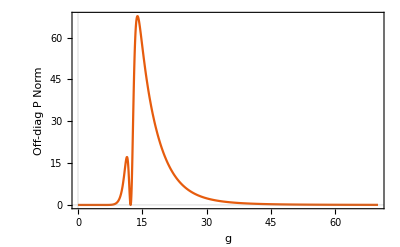

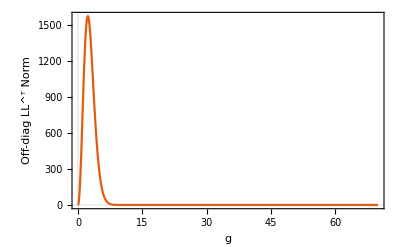

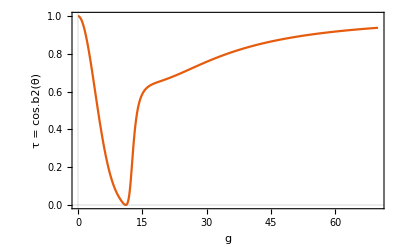

```mathematica
(*param order:[Δo_,ωm_,Δμ_,gom_,gμm_,goμ_]*)
{mS, T} = generateMS[3.1, 5.1, 3.1,g, 11, 0] /. ω -> 0;
p1 =Plot[preIwasawaPlotQND[Re[N[mS/.{g->x}]]],{x,0, 70},PlotRange->Full, PlotTheme->"Scientific", FrameLabel->{"g","Off-diag P Norm"}]
p2=Plot[preIwasawaPlotZ[Re[N[mS/.{g->x}]]],{x,0, 70},PlotRange->Full, PlotTheme->"Scientific", FrameLabel->{"g","Off-diag LL^ᵀ Norm"}]
p3=Plot[preIwasawaPlotBS[Re[N[mS/.{g->x}]]],{x,0, 70},PlotRange->Full, PlotTheme->"Scientific", FrameLabel->{"g","τ = cos.b2(θ)"}]
```